```mathematica
(*This code only works for pos B1, neg B2, but you can change q from positive to negative. This is because each circle has multiple intercepts and it is not worth the effort to account for trajectories of aligned magnetic fields which are not present in the CMS detector*)

Subscript[ϕ, S] = ArcSin[Subscript[R, S]/(2R1)]
x = Simplify[(R1-R2)Sin[2 Subscript[ϕ, S]]]
y= Simplify[R1 - (R1-R2)Cos[2 Subscript[ϕ, S]]]
D2=Simplify[Sqrt[x^2+y^2]]
ϕ[r_] := Simplify[ArcCos[(r^2+D2^2-R2^2)/(r 2 D2 )]]*q 
ϕ[Subscript[R, Sn]]
Subscript[ϕ, 2]=Simplify[ArcTan[y/x]]
phipos[r_]:=Simplify[Subscript[ϕ, 2]+ϕ[r]]
phipos[Subscript[R, Sn]]
```

ArcSin[R_S/(2 R1)]

(R1-R2) Sin[2 ArcSin[R_S/(2 R1)]]

R1+(-R1+R2) Cos[2 ArcSin[R_S/(2 R1)]]

√(R2^2+((R1-R2) R_S^2)/R1)

q ArcCos[(((R1-R2) R_S^2)/R1+R_Sn^2)/(2 √(R2^2+((R1-R2) R_S^2)/R1) R_Sn)]

ArcTan[((R1+(-R1+R2) Cos[2 ArcSin[R_S/(2 R1)]]) Csc[2 ArcSin[R_S/(2 R1)]])/(R1-R2)]

q ArcCos[(((R1-R2) R_S^2)/R1+R_Sn^2)/(2 √(R2^2+((R1-R2) R_S^2)/R1) R_Sn)]+ArcTan[((R1+(-R1+R2) Cos[2 ArcSin[R_S/(2 R1)]]) Csc[2 ArcSin[R_S/(2 R1)]])/(R1-R2)]

1

0.1057

9.46074 √(p^2/(1+89.5056 p^2))

1/(√(1-(89.5056 p^2)/(1+89.5056 p^2)))

4

-1

(0.825 p)/(√(1-(89.5056 p^2)/(1+89.5056 p^2)))

-(3.3 p)/(√(1-(89.5056 p^2)/(1+89.5056 p^2)))

3.55

4.35

5.15

6.2

7.25

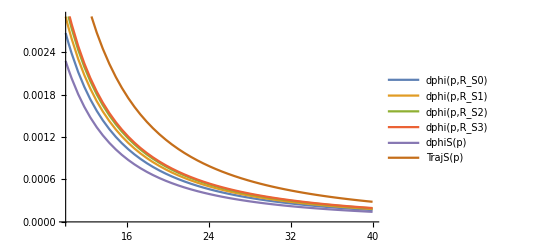

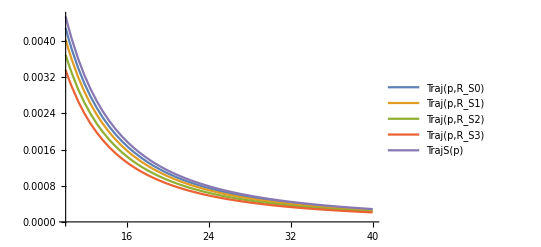

```mathematica
q=1
m=0.1057
(* p=43.28 *)
v = Sqrt[(p/m)^2/(1+(p/m)^2)]
γ=1/Sqrt[1-v^2]
B1=4
B2=-1
R1 = 3.3*(γ p)/(q B1)
R2 = 3.3*(γ p)/(q B2)
Subscript[R, S]= 3.55
Subscript[R, S0]= 4.35
Subscript[R, S1] = 5.15
Subscript[R, S2] = 6.20
Subscript[R, S3] = 7.25

dphi[p_,r_]:=N[Simplify[phipos[r]]]
dphiS[p_]:=N[Simplify[ArcSin[Subscript[R, S]/(2R1)]]]

Traj[p_,r_] :=N[Simplify[ArcTan[(r Sin[phipos[r]]-y)/(r Cos[phipos[r]]-x)]+q*Pi/2]]
TrajS[p_] := 2*dphiS[p]

Plot[{dphi[p, Subscript[R, S0]],dphi[p, Subscript[R, S1]],dphi[p, Subscript[R, S2]],dphi[p, Subscript[R, S3]], dphiS[p],TrajS[p]}, {p,10,40},PlotLegends->"Expressions"]
Plot[{Traj[p,Subscript[R, S0]],Traj[p,Subscript[R, S1]],Traj[p,Subscript[R, S2]],Traj[p,Subscript[R, S3]],TrajS[p]},{p,10,40},PlotLegends->"Expressions"]
```